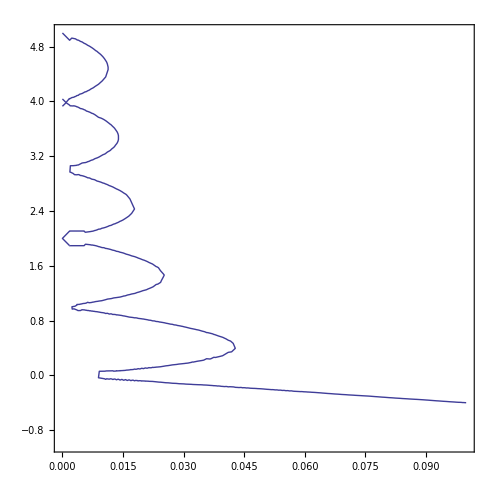
{0.14193,-Graphics-}

```mathematica
number[u_]:=If[u<0,0,Floor[u]+1];
F[w_,mu_]:=4w(1+4 w ((number[mu]+1)/(mu-number[mu])+number[mu]/(number[mu]-1-mu)));
Timing[ContourPlot[F[w,mu]==0,{w,0,0.1},{mu,-1,5},PerformanceGoal->"Quantity"]]
```